# Log analysis 20231001 - 20231007

## Title: CiNiiのログから見るユーザーアクセスグラフの計量分析

## 対象期間：20231001 - 20231007

単日で行った分析結果のsaveを読み込み、1 W分の分析を行う。

## コンセプト

アクセスログから分離したユーザーごとのアクセスグラフを一種のプロダクトとみなし、計量書誌学の観点から分析を行う。

用語：
アクセス：ログのアクセスURL
（アクセス）連鎖：リファラー -> アクセスURLとなる”エッジ”およびエッジが連なった”経路”または”グラフ” => グラフの場合はReferrer Graph[1] というらしい。
ユーザーアクセスグラフ：単一ユーザー（推定）によるアクセスのグラフ
ボキャブラリ：アクセスの性質・アクションを端的に表す単語

分析項目の候補：

ユーザーアクセスグラフの規模クラス内のメンバの分布（Zipを仮定）、1日/1週間/3ヶ月

クラスのメンバ数の分布が対象になるのでクラスを作る。（例：被引用が1件のクラス）

vertex数クラス

edge数クラス

ユーザーの特徴的な行動

リファラーと離脱次のURLのボキャブラリ

ボキャブラリ“detail”が付与される、タイムライン内のノードの位置

ユーザーアクセスグラフの類型

プロパティ：voc出現（重み付き/重みなし）

プロパティ：vocによるアクセスグラフ（重み付き/重みなし）のスペクトル

非対称行列（隣接行列そのまま）のスペクトル

キルヒホフ行列のスペクトル（undirectedの場合重みなしとなる）

N次の連鎖

アクセスグラフの類型ごとのメンバー数がZip型分布に従うか？

アクセスグラフの類型をクラスタリングし類型間の関係を確認する

クラスタリング法は？使用する類型のプロパティは？

分析を組み合わせ、各々の類型がどのような行動パターンか説明可能か？

離脱時のURL(voc)/初回アクセスのリファラー（vocがついていないものあり）

どのくらいのユーザーが”detail”まで確認しているか？

NIIサービス連携がどのくらいあるか？

滞留時間は精度がよくないので発表としては使わない？

タイトル：「CiNiiのログから見るユーザーアクセスグラフの計量分析」

参照：

1. B. de la Ossa, A. Pont, J. Sahuquillo, J. A. Gil ; “Referrer graph: a low-cost web prediction algorithm” ; Proceedings of the 2010 ACM Symposium on Applied ComputingMarch 2010Pages 831–838 ; https://doi.org/10.1145/1774088.1774260

```mathematica
Grid[Import["/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/analysis_items.xlsx"][[1]],ItemSize->Full,Frame->All]
```

CiNiiのログから見るユーザーアクセスグラフの計量分析 |  |  |  |  |  |  |  |  |  |  | 
分析項目の整理 |  |  |  |  |  |  |  |  |  |  | 
 | 分析項目→ | グラフの規模 | グラフのN次の連鎖パス | リファラーと離脱時のアクセスURL(voc) | voc[detail]のグラフ内の位置 | グラフ内のvocの出現 | vocグラフスペクトル | 連携アクセス | 滞在/滞留時間 | [今後]キーワード分析 | [間に合うか？]グラフ使わないクロス集計
 | 目的→ | グラフの規模の分布を確認する | ・各グラフにおける典型的な行動を捉える
・パスの規模の分布を確認する | ・各グラフにおける典型的な行動を捉える | ・ユーザーがdetailページに辿り着いているか | ・グラフを類型化する
・グラフ類型のクラスタリング
・グラフ類型の規模の分布を確認する | ・グラフを類型化する
・グラフ類型のクラスタリング
・グラフ類型の規模の分布を確認する | ・ciと他基盤の連携グラフがどの程度あるか |  |  | 
 | コメント→ |  |  |  |  | 0/1出現を利用してクラスを決定
クラスを対象としてクラスタリング | グラフの固有値列を用いてクラスを決定
クラスを対象としてクラスタリング |  |  |  | ・リファラーと...
・組織と...
 | グラフタイプ↓/グラフから何を確認すれば良いか→ |  |  |  |  |  |  |  |  |  | 
 | Basic-graph
リファラー -> アクセスURLの連鎖による有向グラフ | - | - | - | - | - | - | - |  |  | 
 | voc-label-graph
上記のグラフのvertexにvocを付与したもの | ・Vertex
・Edge | ・最大連鎖長をグラフごとに取る
・1次（Vertex）
・2次（Edge）
・3次
・何次まで？ | ・グラフ内の最初のリファラー
・グラフ内で最後にアクセスしたURL(voc) | ・グラフ内のvertexを最終アクセス時刻順に並べてdetailがどの位置にあるか | ・重みつきvocリスト
・重みなしvocリスト | - | ・条件付きエッジ（リファラーもしくはリクエストURLのvocがci以外を含む、かつciを含む） |  | ・グラフの滞留時間
・ページ滞在時間 | 
 | voc-graph
上記のグラフのvertexをすべてvocに振り直してシュリンクさせたもの | - | - | - |  | - | ・キルヒホフグラフの固有値列 | - |  |  | 
 | Saveの対象
(N) | ・Vertex数
・Edge数
(N=グラフ数) | ・voc-label-graphそのもの
・[保留]voc-label-graphのlongest-path
・voc-graphそのもの
(N=グラフ数) | ・各グラフの最初のリファラーと最後のアクセスURL(要素数:2)
・上記に対するvoc(要素数:2)
(N=グラフ数) | ・各グラフのvertexリストの最終アクセス時刻順
・上記に対するvoc
・vocが"detail"であるposition
(N=グラフ数) | ・重みつきvoc出現リスト(要素数固定ベクトル)
・重みなしvoc出現リスト(要素数固定ベクトル)
(N=グラフ数) | ・キルヒホフ行列
・キルヒホフ行列の固有値列
(N=グラフ数) |  |  |  |

## Target ID

```mathematica
tIDs=Table[n,{n,7}]
```

{1,2,3,4,5,6,7}

## Settings

```mathematica
basedir="/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/

```mathematica
datadir=basedir<>"D=*/T=4/_story/"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=*/T=4/_story/

```mathematica
fileDirs=FileNames[datadir]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231008/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231009/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231010/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231011/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231012/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231013/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231014/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231015/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231016/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231017/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231018/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231019/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231020/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231021/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231022/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231023/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231024/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231025/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231026/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231027/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231028/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231029/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231030/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231031/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231101/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231102/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231103/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231104/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231105/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231106/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231107/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231108/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231109/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231110/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231111/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231112/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231113/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231114/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231115/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231116/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231117/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231118/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231119/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231120/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231121/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231122/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231123/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231124/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231125/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231126/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231127/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231128/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231129/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231130/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231201/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231202/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231203/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231204/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231205/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231206/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231207/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231208/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231209/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231210/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231211/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231212/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231213/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231214/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231215/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231216/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231217/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231218/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231219/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231220/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231221/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231222/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231223/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231224/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231225/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231226/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231227/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231228/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231229/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231230/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231231/T=4/_story}

```mathematica
fileDates=Map[StringSplit[#,{"/","="}][[10]]&,fileDirs]
```

{20231001,20231002,20231003,20231004,20231005,20231006,20231007,20231008,20231009,20231010,20231011,20231012,20231013,20231014,20231015,20231016,20231017,20231018,20231019,20231020,20231021,20231022,20231023,20231024,20231025,20231026,20231027,20231028,20231029,20231030,20231031,20231101,20231102,20231103,20231104,20231105,20231106,20231107,20231108,20231109,20231110,20231111,20231112,20231113,20231114,20231115,20231116,20231117,20231118,20231119,20231120,20231121,20231122,20231123,20231124,20231125,20231126,20231127,20231128,20231129,20231130,20231201,20231202,20231203,20231204,20231205,20231206,20231207,20231208,20231209,20231210,20231211,20231212,20231213,20231214,20231215,20231216,20231217,20231218,20231219,20231220,20231221,20231222,20231223,20231224,20231225,20231226,20231227,20231228,20231229,20231230,20231231}

```mathematica
vocdir="/Volumes/home/NII/togo-log/rcoslogs/voc/"
```

/Volumes/home/NII/togo-log/rcoslogs/voc/

## Edge & Vertex from voc-label graph

### エッジ+ノードカウントデータ

```mathematica
EVSaveFile=Table[fileDirs[[tIDs[[n]]]]<>"/log-analysis_"<>fileDates[[tIDs[[n]]]]<>"_EVcount.save",{n,Length[tIDs]}]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story/log-analysis_20231002_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story/log-analysis_20231003_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story/log-analysis_20231004_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story/log-analysis_20231005_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story/log-analysis_20231006_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story/log-analysis_20231007_EVcount.save}

```mathematica
start=Now
Map[Get,EVSaveFile];
end=Now
end-start
```

Fri 1 Mar 2024 18:18:18GMT+9

Part::partw: Part 3 of {porntrex.com} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Fri 1 Mar 2024 18:20:27GMT+9

2.15505 min

### edge count

```mathematica
(storyEdgeSelW[4,"voc-edgecount"]["20231001-07"]=Apply[Join,Map[storyEdgeSel[4,"voc-edgecount"][fileDates[[#]]]&,tIDs]])//Dimensions
```

{1143117}

エッジ数そのもののZipf分布(N(r)=C r^-a)を「一応」確認する：
aは1~3程度が通常、aが小さいほど均等。aはここから乖離しても構わない。

```mathematica
Remove[a,c];
zipf[r_]:=c r^(-a);
zipffitW[4,"graph_edge"]["20231001-07"]=FindFit[Sort[storyEdgeSelW[4,"voc-edgecount"]["20231001-07"],#1>#2&],zipf[r],{c,a},r]
```

{c→11071.5,a→0.583885}

エッジ数クラスのメンバ数のZipf分布(N(r)=C r^-a)を確認する：
aは1~3程度が通常、aが小さいほど均等。

```mathematica
tallysortW[4,"voc-edgecount-prod"]["20231001-07"]=Sort[Tally[storyEdgeSelW[4,"voc-edgecount"]["20231001-07"]],#1[[2]]>#2[[2]]&]
```

{{1,809861},{2,84994},{3,57745},{4,29174},{5,24521},{6,16204},{7,14303},{8,10741},{9,9417},{10,7785},{11,6866},{12,5782},{13,5354},{14,4412},{15,4182},{16,3557},{17,3348},{18,2978},{19,2722},{20,2425},{21,2219},{22,1890},{23,1797},{24,1733},{25,1592},{26,1341},{27,1328},{28,1185},{29,1105},{30,964},{31,962},{32,908},{33,853},{34,797},{35,690},{37,686},{36,672},{38,628},{39,584},{41,506},{40,502},{43,481},{44,472},{42,467},{46,393},{45,370},{48,354},{47,354},{49,343},{50,340},{54,307},{52,304},{53,292},{51,288},{55,273},{57,249},{56,243},{58,234},{61,221},{60,219},{59,207},{63,194},{64,194},{69,179},{62,173},{67,168},{66,164},{65,160},{68,160},{71,136},{72,133},{70,128},{76,123},{75,115},{73,112},{77,110},{74,104},{79,103},{80,95},{81,90},{78,89},{84,84},{82,79},{85,77},{87,75},{83,74},{89,71},{86,70},{96,70},{98,70},{91,69},{93,68},{105,66},{88,66},{90,61},{92,61},{107,59},{100,59},{95,56},{97,54},{99,53},{101,52},{94,50},{106,49},{102,46},{104,45},{112,45},{111,42},{103,40},{125,39},{122,39},{114,37},{108,37},{110,36},{117,35},{120,34},{115,33},{119,32},{131,32},{123,32},{121,31},{135,30},{116,29},{126,29},{118,29},{128,29},{130,28},{113,28},{127,28},{124,28},{144,26},{149,25},{133,24},{161,24},{151,24},{150,23},{138,23},{109,22},{153,22},{141,21},{142,21},{140,21},{134,20},{139,20},{137,20},{145,20},{132,19},{156,19},{160,18},{192,17},{183,17},{129,17},{166,17},{146,17},{148,17},{165,16},{182,16},{170,16},{185,16},{162,16},{172,16},{184,15},{158,15},{173,15},{159,15},{288,15},{147,15},{154,15},{212,14},{155,14},{152,14},{157,14},{136,14},{177,13},{143,13},{189,13},{241,12},{225,12},{195,12},{168,12},{206,12},{174,12},{164,12},{190,11},{191,11},{188,11},{236,11},{179,11},{220,11},{222,11},{186,11},{219,11},{198,10},{232,10},{226,10},{230,10},{221,10},{169,10},{163,10},{176,9},{229,9},{171,9},{218,9},{178,9},{207,9},{181,9},{223,9},{205,9},{203,9},{201,9},{175,9},{213,9},{167,9},{204,8},{209,8},{239,8},{187,8},{266,8},{216,8},{215,8},{208,8},{196,8},{194,7},{318,7},{258,7},{231,7},{233,7},{228,7},{248,7},{278,7},{180,6},{491,6},{211,6},{280,6},{286,6},{327,6},{237,6},{299,6},{210,6},{323,6},{263,6},{199,6},{279,6},{240,6},{244,6},{317,6},{245,5},{303,5},{324,5},{243,5},{403,5},{493,5},{336,5},{330,5},{227,5},{268,5},{247,5},{250,5},{271,5},{238,5},{302,5},{292,5},{343,4},{305,4},{332,4},{602,4},{350,4},{224,4},{200,4},{519,4},{316,4},{331,4},{532,4},{261,4},{281,4},{313,4},{217,4},{256,4},{253,4},{363,4},{340,4},{356,4},{197,4},{193,4},{329,4},{319,4},{254,4},{293,4},{528,4},{264,4},{249,4},{272,4},{282,4},{274,4},{354,4},{246,4},{306,4},{270,4},{1365,3},{432,3},{504,3},{287,3},{267,3},{311,3},{355,3},{398,3},{314,3},{799,3},{820,3},{424,3},{533,3},{490,3},{526,3},{360,3},{391,3},{367,3},{733,3},{470,3},{300,3},{358,3},{214,3},{259,3},{295,3},{290,3},{285,3},{434,3},{235,3},{297,3},{257,3},{431,3},{576,3},{255,3},{445,3},{301,3},{409,3},{401,3},{353,3},{433,3},{284,3},{308,3},{387,3},{406,3},{443,3},{309,3},{307,3},{339,3},{291,3},{558,3},{364,3},{562,3},{654,3},{641,3},{454,3},{251,3},{275,3},{485,3},{645,3},{372,2},{549,2},{728,2},{1377,2},{411,2},{351,2},{991,2},{996,2},{525,2},{461,2},{334,2},{373,2},{333,2},{1087,2},{260,2},{704,2},{5312,2},{676,2},{585,2},{545,2},{400,2},{715,2},{492,2},{326,2},{517,2},{322,2},{321,2},{320,2},{506,2},{413,2},{734,2},{312,2},{1081,2},{672,2},{341,2},{589,2},{430,2},{346,2},{294,2},{500,2},{536,2},{520,2},{298,2},{371,2},{553,2},{352,2},{446,2},{601,2},{606,2},{809,2},{283,2},{392,2},{422,2},{952,2},{531,2},{572,2},{265,2},{359,2},{394,2},{202,2},{680,2},{554,2},{644,2},{494,2},{594,2},{735,2},{269,2},{588,2},{829,2},{843,2},{805,2},{234,2},{541,2},{296,2},{368,2},{681,2},{481,2},{410,2},{440,2},{518,2},{345,2},{242,2},{252,2},{575,2},{822,2},{776,2},{667,2},{632,2},{277,2},{469,2},{463,2},{633,2},{276,2},{1281,2},{450,2},{442,2},{486,2},{335,2},{456,2},{586,2},{664,2},{304,2},{857,1},{699,1},{4285,1},{3423,1},{3163,1},{1538,1},{1545,1},{1371,1},{2312,1},{2285,1},{2291,1},{2287,1},{1873,1},{1170,1},{673,1},{273,1},{552,1},{505,1},{435,1},{1450,1},{1363,1},{1639,1},{3696,1},{3641,1},{751,1},{861,1},{361,1},{514,1},{1221,1},{1548,1},{1273,1},{1274,1},{551,1},{670,1},{595,1},{418,1},{420,1},{582,1},{642,1},{503,1},{480,1},{453,1},{1313,1},{404,1},{846,1},{1008,1},{841,1},{535,1},{362,1},{1031,1},{1048,1},{1044,1},{1084,1},{1783,1},{936,1},{938,1},{935,1},{939,1},{945,1},{473,1},{598,1},{635,1},{901,1},{524,1},{627,1},{527,1},{397,1},{474,1},{1211,1},{1203,1},{365,1},{408,1},{388,1},{262,1},{714,1},{438,1},{447,1},{382,1},{848,1},{1035,1},{1024,1},{5327,1},{5311,1},{6060,1},{3617,1},{3606,1},{3610,1},{3936,1},{707,1},{689,1},{1230,1},{1075,1},{452,1},{597,1},{539,1},{484,1},{657,1},{954,1},{502,1},{338,1},{357,1},{437,1},{591,1},{444,1},{344,1},{468,1},{325,1},{608,1},{721,1},{2038,1},{1939,1},{729,1},{399,1},{1006,1},{955,1},{1012,1},{1042,1},{987,1},{374,1},{466,1},{419,1},{412,1},{959,1},{786,1},{797,1},{784,1},{844,1},{510,1},{656,1},{928,1},{976,1},{972,1},{1072,1},{1091,1},{1089,1},{530,1},{777,1},{771,1},{849,1},{666,1},{847,1},{605,1},{655,1},{953,1},{460,1},{618,1},{749,1},{590,1},{4193,1},{4190,1},{570,1},{806,1},{816,1},{543,1},{495,1},{646,1},{783,1},{761,1},{791,1},{1020,1},{482,1},{563,1},{723,1},{467,1},{489,1},{448,1},{649,1},{421,1},{571,1},{663,1},{700,1},{464,1},{538,1},{522,1},{690,1},{709,1},{378,1},{5219,1},{5336,1},{658,1},{607,1},{555,1},{823,1},{795,1},{833,1},{427,1},{426,1},{425,1},{416,1},{479,1},{436,1},{1339,1},{1195,1},{1184,1},{1412,1},{1186,1},{750,1},{917,1},{731,1},{752,1},{669,1},{675,1},{439,1},{616,1},{615,1},{725,1},{349,1},{417,1},{1329,1},{1307,1},{289,1},{648,1},{337,1},{599,1},{380,1},{564,1},{637,1},{698,1},{1406,1},{1888,1},{1646,1},{684,1},{910,1},{895,1},{370,1},{556,1},{548,1},{634,1},{1047,1},{1037,1},{611,1},{579,1},{386,1},{414,1},{636,1},{455,1},{1344,1},{477,1},{458,1},{619,1},{629,1},{652,1},{1678,1},{3020,1},{348,1}}

```mathematica
Remove[a,c];
zipf[r_]:=c r^(-a);
zipffitW[4,"edge"]["20231001-07"]=FindFit[Map[#[[2]]&,tallysortW[4,"voc-edgecount-prod"]["20231001-07"]],zipf[r],{c,a},r]
```

{c→808478.,a→2.9119}

### vertex count

```mathematica
storyNodeSel[4,"voc-nodecount"][fileDates[[2]]]//Length
```

183802

```mathematica
(storyNodeSelW[4,"voc-nodecount"]["20231001-07"]=Apply[Join,Map[storyNodeSel[4,"voc-nodecount"][fileDates[[#]]]&,tIDs]])//Length
```

1143117

ノード数クラスのメンバ数のZipf分布(N(r)=C r^-a)を確認する：
aは1~3程度が通常、aが小さいほど均等。

```mathematica
tallysortW[4,"voc-nodecount-prod"]["20231001-07"]=Sort[Tally[storyNodeSelW[4,"voc-nodecount"]["20231001-07"]],#1[[2]]>#2[[2]]&]
```

{{2,852134},{3,99663},{4,45115},{5,27304},{6,19441},{7,14295},{8,11325},{9,8878},{10,7263},{11,6248},{12,5124},{13,4576},{14,3836},{15,3341},{16,2951},{17,2644},{18,2315},{19,2033},{20,1780},{21,1713},{22,1471},{23,1293},{24,1154},{25,1087},{26,948},{27,840},{28,763},{29,694},{30,670},{31,642},{32,554},{33,544},{34,491},{35,452},{36,438},{37,409},{38,364},{39,355},{40,340},{42,293},{41,288},{43,278},{45,251},{44,250},{47,233},{46,212},{48,211},{49,199},{50,184},{51,179},{54,172},{52,147},{55,145},{53,138},{58,127},{59,125},{57,122},{56,121},{61,108},{60,106},{63,103},{64,96},{65,94},{62,82},{66,77},{68,74},{69,72},{67,70},{76,68},{70,68},{71,67},{72,67},{77,63},{80,62},{74,61},{75,59},{83,58},{89,53},{78,50},{87,49},{82,48},{73,47},{84,46},{79,45},{85,43},{81,42},{98,36},{90,36},{97,35},{94,35},{88,34},{91,34},{86,34},{95,34},{103,33},{92,31},{99,27},{96,27},{107,27},{106,26},{112,25},{101,25},{116,24},{121,24},{102,23},{113,23},{93,23},{100,22},{117,22},{115,21},{108,21},{109,20},{124,20},{105,20},{118,19},{122,18},{128,18},{119,18},{132,18},{126,17},{120,17},{111,17},{134,17},{152,16},{137,16},{157,16},{127,15},{131,15},{104,15},{125,14},{130,14},{136,13},{149,13},{151,13},{110,12},{123,12},{129,12},{114,12},{154,11},{146,11},{133,11},{138,11},{197,11},{171,10},{158,10},{182,10},{135,10},{141,9},{153,9},{148,9},{164,9},{159,9},{150,9},{160,9},{140,9},{205,8},{167,8},{155,8},{206,8},{147,8},{245,8},{186,8},{184,7},{239,7},{166,7},{188,7},{144,7},{176,7},{248,7},{198,7},{173,7},{145,7},{170,7},{223,7},{161,6},{180,6},{356,6},{143,6},{169,6},{174,6},{177,6},{227,6},{285,6},{229,6},{637,5},{190,5},{236,5},{163,5},{300,5},{355,5},{269,5},{156,5},{199,5},{315,5},{222,5},{289,5},{228,5},{241,5},{193,5},{275,5},{232,5},{221,5},{142,5},{139,5},{299,5},{282,4},{243,4},{246,4},{218,4},{293,4},{365,4},{298,4},{201,4},{214,4},{224,4},{194,4},{266,4},{178,4},{217,4},{187,4},{172,4},{185,4},{238,4},{314,4},{195,4},{341,4},{262,4},{200,4},{283,4},{528,3},{207,3},{304,3},{226,3},{231,3},{168,3},{444,3},{302,3},{183,3},{442,3},{278,3},{307,3},{274,3},{263,3},{219,3},{446,3},{294,3},{306,3},{286,3},{374,3},{208,3},{204,3},{301,3},{181,3},{179,3},{418,3},{305,3},{327,3},{318,3},{216,3},{212,3},{213,3},{165,3},{196,3},{209,3},{287,3},{268,3},{291,3},{401,3},{230,3},{202,3},{297,3},{288,3},{259,3},{376,2},{527,2},{364,2},{233,2},{3082,2},{372,2},{253,2},{311,2},{320,2},{220,2},{203,2},{175,2},{235,2},{447,2},{475,2},{386,2},{379,2},{565,2},{296,2},{225,2},{192,2},{162,2},{340,2},{272,2},{240,2},{258,2},{234,2},{309,2},{295,2},{215,2},{303,2},{330,2},{445,2},{271,2},{371,2},{362,2},{383,2},{256,2},{281,2},{250,2},{352,2},{310,2},{308,2},{290,2},{265,2},{317,2},{428,2},{566,2},{321,2},{342,2},{284,2},{247,2},{189,2},{334,2},{210,2},{273,2},{396,2},{706,1},{573,1},{930,1},{257,1},{261,1},{454,1},{981,1},{497,1},{468,1},{2469,1},{2440,1},{548,1},{508,1},{1153,1},{1454,1},{596,1},{597,1},{211,1},{346,1},{347,1},{1067,1},{255,1},{354,1},{397,1},{1037,1},{462,1},{470,1},{337,1},{536,1},{545,1},{541,1},{368,1},{437,1},{358,1},{384,1},{412,1},{422,1},{894,1},{615,1},{3089,1},{3081,1},{3235,1},{2173,1},{2168,1},{2169,1},{2200,1},{331,1},{363,1},{561,1},{563,1},{312,1},{252,1},{410,1},{619,1},{818,1},{421,1},{435,1},{251,1},{279,1},{486,1},{494,1},{270,1},{237,1},{467,1},{461,1},{377,1},{339,1},{487,1},{829,1},{620,1},{381,1},{385,1},{404,1},{366,1},{476,1},{640,1},{645,1},{646,1},{623,1},{633,1},{351,1},{522,1},{453,1},{458,1},{349,1},{249,1},{242,1},{403,1},{432,1},{675,1},{860,1},{316,1},{326,1},{369,1},{353,1},{375,1},{191,1},{276,1},{599,1},{325,1},{691,1},{373,1},{459,1},{822,1},{828,1},{323,1},{387,1},{390,1},{1077,1},{704,1},{806,1},{705,1},{493,1},{343,1},{852,1},{1042,1},{471,1},{361,1},{388,1},{277,1},{1114,1},{324,1},{1119,1},{968,1},{577,1},{280,1},{333,1},{348,1},{405,1},{244,1},{335,1},{996,1},{1079,1}}

```mathematica
Remove[a,c];
zipf[r_]:=c r^(-a);
zipffitW[4,"node"]["20231001-07"]=FindFit[Map[#[[2]]&,tallysortW[4,"voc-nodecount-prod"]["20231001-07"]],zipf[r],{c,a},r]
```

{c→851283.,a→2.91675}

### time-sorted vertex(mintime)

vocリスト中のdetailの位置

```mathematica
(vocDetailPosW[4]["20231001-07"]=Apply[Join,Map[vocDetailPos[4][fileDates[[#]]]&,tIDs]])//Length
```

1143117

およそ1割がdetailに到達しておらず、

```mathematica
(vocNoDetailPosW[4]["20231001-07"]=Sort[Cases[vocDetailPosW[4]["20231001-07"],x_/;x[[2]]=={}],#1[[1]]>#2[[1]]&])//Length
```

106525

さらにそのおよそ1割が多量アクセスを行っている。

```mathematica
Cases[vocNoDetailPosW[4]["20231001-07"],x_/;x[[1]]>=10]//Length
```

6613

### first-in last-out

グラフの最初のリファラー(ドメイン)と離脱次のvocのペア

```mathematica
storyNodePSel[4,"firstANDlast","voc","dropAccT","domain"][fileDates[[2]]]//Length
```

183802

```mathematica
(storyNodePSelW[4,"firstANDlast","voc","dropAccT","domain"]["20231001-07"]=Apply[Join,Map[storyNodePSel[4,"firstANDlast","voc","dropAccT","domain"][fileDates[[#]]]&,tIDs]])//Length
```

1143117

In - Out集計

```mathematica
(storyNodeInOutClassW[4]["20231001-07"]=Sort[Tally[storyNodePSelW[4,"firstANDlast","voc","dropAccT","domain"]["20231001-07"]],#1[[2]]>#2[[2]]&])//Dimensions
```

{6950,2}

```mathematica
storyNodeInOutClassW[4]["20231001-07"][[1;;100]]
```

{{{ci.nii.ac.jp,voc[ci:*,confirm,detail]},331229},{{www.google.com,voc[ci:*,confirm,detail]},193260},{{www.google.co.jp,voc[ci:*,confirm,detail]},91211},{{search.yahoo.co.jp,voc[ci:*,confirm,detail]},73609},{{scholar.google.com,voc[ci:*,confirm,detail]},65901},{{www.bing.com,voc[ci:*,confirm,detail]},41194},{{scholar.google.co.jp,voc[ci:*,confirm,detail]},29104},{{voc[ci:*,view,top],voc[ci:*,explore,all]},26735},{{voc[ci:*,explore,all],voc[ci:*,explore,all]},24533},{{www.google.com,voc[ci:*,explore,all]},17323},{{voc[ci:*,explore,all],voc[ci:*,confirm,detail]},17028},{{voc[ci:*,confirm,detail],voc[ci:*,confirm,detail]},14674},{{voc[ci:*,view,top],voc[ci:*,confirm,detail]},13130},{{search.jamas.or.jp,voc[ci:*,confirm,detail]},9814},{{voc[ci:*,search,articles],voc[ci:*,search,articles]},9770},{{www.google.com,voc[ci:*,view,top]},9536},{{www.bing.com,voc[ci:*,explore,all]},7059},{{www.google.co.jp,voc[ci:*,explore,all]},6639},{{kaken.nii.ac.jp,voc[ci:*,confirm,detail]},5934},{{ci.nii.ac.jp,voc[ci:*,view,top]},5879},{{voc[ci:*,confirm,detail],voc[ci:*,explore,all]},5837},{{voc[ci:*,search,articles],voc[ci:*,confirm,detail]},5680},{{voc[ci:*,view,top],voc[ci:*,search,articles]},5174},{{iss.ndl.go.jp,voc[ci:*,view,top]},4964},{{ci.nii.ac.jp,voc[ci:*,search,articles]},4841},{{www.google.co.jp,voc[ci:*,view,top]},4495},{{scholar.google.jp,voc[ci:*,confirm,detail]},4406},{{www.google.com,voc[ci:*,search,articles]},3858},{{search.yahoo.co.jp,voc[ci:*,explore,all]},3522},{{nrid.nii.ac.jp,voc[ci:*,confirm,detail]},3211},{{scholar.google.es,voc[ci:*,confirm,detail]},2975},{{t.co,voc[ci:*,confirm,detail]},2916},{{voc[ci:*,explore,all],voc[ci:*,search,articles]},2789},{{www.bing.com,voc[ci:*,search,articles]},2416},{{www.wikidata.org,voc[ci:*,confirm,detail]},2400},{{scholar.google.de,voc[ci:*,confirm,detail]},2042},{{search.yahoo.co.jp,voc[ci:*,view,top]},1835},{{voc[ci:*,request,api],voc[ci:*,search,articles]},1659},{{www.bing.com,voc[ci:*,view,top]},1601},{{www.google.co.jp,voc[ci:*,search,articles]},1564},{{scholar.google.com,voc[ci:*,explore,all]},1538},{{www.google.com,voc[ci:*,request,resourcesync]},1505},{{sc.panda321.com,voc[ci:*,confirm,detail]},1319},{{scholar.google.com.br,voc[ci:*,confirm,detail]},1163},{{scholar.google.com.au,voc[ci:*,confirm,detail]},1157},{{scholar.google.com.hk,voc[ci:*,confirm,detail]},1117},{{researchmap.jp,voc[ci:*,confirm,detail]},1097},{{duckduckgo.com,voc[ci:*,confirm,detail]},1051},{{m.wikidata.org,voc[ci:*,confirm,detail]},913},{{ja.wikipedia.org,voc[ci:*,confirm,detail]},868},{{tripitaka.l.u-tokyo.ac.jp,voc[ci:*,confirm,detail]},844},{{voc[ci:*,confirm,detail],voc[ci:*,search,articles]},820},{{cn.bing.com,voc[ci:*,confirm,detail]},812},{{scholar.google.com.tw,voc[ci:*,confirm,detail]},804},{{search.yahoo.co.jp,voc[ci:*,search,articles]},746},{{www.google.com.hk,voc[ci:*,confirm,detail]},745},{{scholar.google.co.jp,voc[ci:*,explore,all]},725},{{ci.nii.ac.jp,voc[ci:*,explore,all]},698},{{service.smt.docomo.ne.jp,voc[ci:*,confirm,detail]},691},{{scholar.google.co.uk,voc[ci:*,confirm,detail]},679},{{scholar.google.co.kr,voc[ci:*,confirm,detail]},662},{{scholar.google.gr,voc[ci:*,confirm,detail]},653},{{voc[ci:*,search,articles],voc[ci:*,explore,all]},650},{{csweb.ibaraki.ac.jp,voc[ci:*,confirm,detail]},604},{{ja.m.wikipedia.org,voc[ci:*,explore,all]},595},{{ci.nii.ac.jp:443,voc[ci:*,view,top]},556},{{voc[ci:*,view,top],voc[ci:*,search,books]},554},{{kango-sakuin.nurse.or.jp,voc[ci:*,confirm,detail]},551},{{ja.m.wikipedia.org,voc[ci:*,confirm,detail]},535},{{ja.wikipedia.org,voc[ci:*,explore,all]},446},{{so1.cljtscd.com,voc[ci:*,confirm,detail]},420},{{websearch.rakuten.co.jp,voc[ci:*,confirm,detail]},418},{{search.jamas.or.jp,voc[ci:*,explore,all]},416},{{voc[ci:*,explore,all],voc[ci:*,view,top]},392},{{scholar.google.co.id,voc[ci:*,confirm,detail]},388},{{www.gproxx.com,voc[ci:*,confirm,detail]},381},{{www.google.com,voc[ci:*,search,books]},354},{{voc[ci:*,search,books],voc[ci:*,confirm,detail]},349},{{scholar.google.ca,voc[ci:*,confirm,detail]},346},{{runners.ritsumei.ac.jp,voc[ci:*,confirm,detail]},333},{{www.tulips.tsukuba.ac.jp,voc[ci:*,confirm,detail]},329},{{iss.ndl.go.jp,voc[ci:*,explore,all]},327},{{altmetrics.ceek.jp,voc[ci:*,confirm,detail]},324},{{nmsrdb.nms.ac.jp,voc[ci:*,confirm,detail]},317},{{voc[ci:*,search,books],voc[ci:*,search,books]},301},{{voc[ci:*,explore,all],voc[ci:*,search,books]},301},{{scholar.google.fr,voc[ci:*,confirm,detail]},283},{{cn.bing.com,voc[ci:*,explore,all]},276},{{cir.nii.ac.jp,voc[ci:*,confirm,detail]},273},{{voc[ci:*,view,top],voc[ci:*,search,dssertations]},264},{{ci.nii.ac.jp:443,voc[ci:*,confirm,detail]},263},{{so2.cljtscd.com,voc[ci:*,confirm,detail]},256},{{so3.cljtscd.com,voc[ci:*,confirm,detail]},248},{{scholar.google.ru,voc[ci:*,confirm,detail]},225},{{opac.lib.kansai-u.ac.jp,voc[ci:*,confirm,detail]},222},{{{}⟦3⟧,voc[ci:*,confirm,detail]},214},{{altmetrics.ceek.jp,voc[ci:*,view,top]},209},{{ja.wikipedia.org,voc[ci:*,search,articles]},207},{{kids.yahoo.co.jp,voc[ci:*,confirm,detail]},205},{{www.google.co.kr,voc[ci:*,confirm,detail]},204}}

### vocベクトルデータ

```mathematica
vocVecSaveFile=Table[fileDirs[[tIDs[[n]]]]<>"/log-analysis_"<>fileDates[[tIDs[[n]]]]<>"_vocVec.save",{n,Length[tIDs]}]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story/log-analysis_20231002_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story/log-analysis_20231003_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story/log-analysis_20231004_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story/log-analysis_20231005_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story/log-analysis_20231006_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story/log-analysis_20231007_vocVec.save}

```mathematica
Get[vocVecSaveFile[[2]]];
```

```mathematica
start=Now
Map[Get,vocVecSaveFile];
end=Now
end-start
```

Fri 1 Mar 2024 18:21:16GMT+9

Fri 1 Mar 2024 18:24:43GMT+9

3.45088 min

### voc vector

```mathematica
storyVocAVecSel[4,"voc-only"][fileDates[[2]]]//Length
```

183802

重みなし(0/1)voc出現リスト

```mathematica
(storyVocAVecSelW[4,"voc-only"]["20231001-07"]=Apply[Join,Map[storyVocAVecSel[4,"voc-only"][fileDates[[#]]]&,tIDs]])//Dimensions
```

{1143117,59}

Tallyでクラスを作る

```mathematica
(storyVocAVecSelClassW[4,"voc-only"]["20231001-07"]=Sort[Tally[storyVocAVecSelW[4,"voc-only"]["20231001-07"]],#1[[2]]>=#2[[2]]&])//Dimensions
```

{498,2}

```mathematica
(storyVocAVecSelClassW[4,"voc-only","top50"]["20231001-07"]=storyVocAVecSelClassW[4,"voc-only"]["20231001-07"][[1;;50]])//Dimensions
```

{50,2}

### voc vectorクラスタリング

クラスタリング前の分布の確認

すべてのクラス

```mathematica
(storyVocAVecSelClassPCAW[4,"voc-only"]["20231001-07"]=PrincipalComponents[N[Map[#[[1]]&,storyVocAVecSelClassW[4,"voc-only"]["20231001-07"]]]])//Dimensions
```

{498,59}

```mathematica
Graphics3D[Map[Point[#[[1;;3]]]&,storyVocAVecSelClassPCAW[4,"voc-only"]["20231001-07"]]]
```

-Graphics3D-

メンバーの多いクラス上位50

```mathematica
(storyVocAVecSelClassPCAW[4,"voc-only","top50"]["20231001-07"]=PrincipalComponents[N[Map[#[[1]]&,storyVocAVecSelClassW[4,"voc-only","top50"]["20231001-07"]]]])//Dimensions
```

{50,59}

```mathematica
Graphics3D[Map[Point[#[[1;;3]]]&,storyVocAVecSelClassPCAW[4,"voc-only","top50"]["20231001-07"]]]
```

-Graphics3D-

上位50クラスを階層クラスタリング

### 滞在・滞留時間データ

```mathematica
accTimeSaveFile=Table[fileDirs[[tIDs[[n]]]]<>"/log-analysis_"<>fileDates[[tIDs[[n]]]]<>"_accTime.save",{n,Length[tIDs]}]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story/log-analysis_20231002_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story/log-analysis_20231003_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story/log-analysis_20231004_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story/log-analysis_20231005_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story/log-analysis_20231006_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story/log-analysis_20231007_accTime.save}

```mathematica
start=Now
Map[Get,accTimeSaveFile];
end=Now
end-start
```

Sun 3 Mar 2024 20:20:53GMT+9

Sun 3 Mar 2024 20:21:05GMT+9

12.3285 s

```mathematica
(edgeAccTimeListW[4]["20231001-07"]=Apply[Join,Map[edgeAccTimeList[4,"stay"][fileDates[[#]]]&,tIDs]])//Dimensions
```

{1143117}

## KirchhoffMatrix from voc graph

### キルヒホフ行列データ

```mathematica
KMSaveFile=Table[fileDirs[[tIDs[[n]]]]<>"/log-analysis_"<>fileDates[[tIDs[[n]]]]<>"_KM.save",{n,Length[tIDs]}]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story/log-analysis_20231002_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story/log-analysis_20231003_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story/log-analysis_20231004_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story/log-analysis_20231005_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story/log-analysis_20231006_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story/log-analysis_20231007_KM.save}

```mathematica
start=Now
Map[Get,KMSaveFile];
end=Now
end-start
```

Fri 1 Mar 2024 18:24:46GMT+9

Fri 1 Mar 2024 18:34:43GMT+9

9.94972 min

### 固有値によるクラスタリング

キルヒホフ行列の固有値列

```mathematica
(storyVocGraphEva59W[4]["20231001-07"]=Apply[Join,Map[storyVocGraphEva59[4][fileDates[[#]]]&,tIDs]])//Dimensions
```

{1143117,59}

Tallyでクラスをつくる

```mathematica
(storyVocGraphEva59CLassW[4]["20231001-07"]=Tally[storyVocGraphEva59W[4]["20231001-07"]])//Dimensions
```

{6510,2}

クラスの固有値列のPCA

```mathematica
Eva59ClassNum=(storyVocGraphEva59CLassPCAW[4]["20231001-07"]=PrincipalComponents[Map[#[[1]]&,storyVocGraphEva59CLassW[4]["20231001-07"]]])//Length
```

6510

```mathematica
Graphics3D[Map[Point[#[[1;;3]]]&,storyVocGraphEva59CLassPCAW[4]["20231001-07"]]]
```

-Graphics3D-

クラスタリング

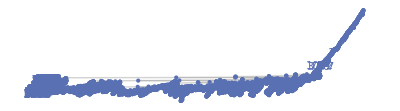

```mathematica
CT=ClusteringTree[   N[Map[#[[1]]&,storyVocGraphEva59CLassW[4]["20231001-07"]]]   ->Table[n,{n,Eva59ClassNum}]   ]
```